```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957061;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

```mathematica
(*τ->3π*)
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H=SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1,m1];
cH=ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=Sqrt[1-((m2+Sqrt[q2])/m1)^2]*Sqrt[1-((m2-Sqrt[q2])/m1)^2];
HT:=λ*H4;
HT;
Fq3π1=2.93*10^-5*((q2-9*mπ^2)/q2)^4*(1+190 q2)/((q2-1.06)^2+0.48)^2;
Fq3π=(0.000058592966004157997*(-0.17640000000000003+q2)^4*(1+1.510651725804281*^-105*q2+189.45911486214024*q2^2))/((0.48273650253772327+(-1.0373349238887504+q2)^2)^2*q2^4)/2;
dΓ3π=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3π;
dΓ3π1=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3π1;
(*Decay to 3π*)
m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
Const3π=1;
Γ3π=NIntegrate[dΓ3π,{q2,9 mπ^2,(m1-m2)^2}];
Clear[Const3π];
Br=Γ3π/Γτ;
BrNorm=0.0903;
Const3π=BrNorm/Br
Γ3π=Const3π*NIntegrate[dΓ3π,{q2,9 mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Error=Br/BrNorm
```

1.34154

1.

## Clear

```mathematica
Clear[Fq3π1,Fq2π,Fq3π,Fq4π,Fq5π,Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ3π1,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4, Fq3π,Fq5π,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
Fq3π=Const3π*(0.000058592966004157997*(-0.17640000000000003+m232)^4*(1+1.510651725804281*^-105*m232+189.45911486214024*m232^2))/((0.48273650253772327+(-1.0373349238887504+m232)^2)^2*m232^4)/2;
Fq3π1:=Const3π*2.93*10^-5*((m232-9*mπ^2)/m232)^4*(1+190 m232)/((m232-1.06)^2+0.48)^2;
dΓ3π:=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq3π;
dΓ3π1:=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq3π1;
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Test

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Omega_{c}^{0}";
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
m1= 3.78663;
m2= 2.6952;
picOmega= Plot[dΓ3π*y/y0,{m232,9 mπ^2,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
f1
```

0.3675/(0.060898 m232^2-0.405696 m232+1)-1.122/(0.0257202 m232^2-0.308642 m232+1)

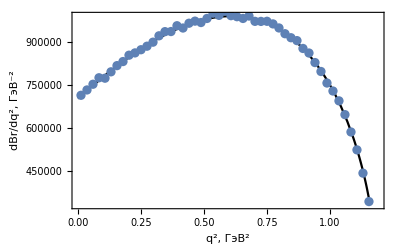

```mathematica
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab=ReadList["m2_23.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
{x,y}={tab[[10,1]],tab[[10,2]]};
y0=dΓl/.m232-> x;
pic1= Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab];
Show[pic1, pic2]
```

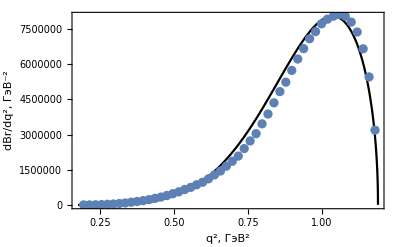

```mathematica
(*Файл с 3000000 распадов, который долго считается*)
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab=ReadList["m2_234_3000000.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
{x,y}={tab[[43,1]],tab[[43,2]]};
y0=dΓ3π/.m232-> x;
pic1 = Plot[dΓ3π*y/y0,{m232,9 mπ^2,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab];
Show[pic1, pic2]
```

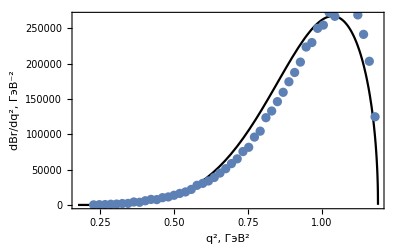

```mathematica
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab=ReadList["m2_234.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
{x,y}={tab[[43,1]],tab[[43,2]]};
y0=dΓ3π/.m232-> x;
pic1= Plot[dΓ3π*y/y0,{m232,9 mπ^2,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab];
Show[pic1, pic2]
```

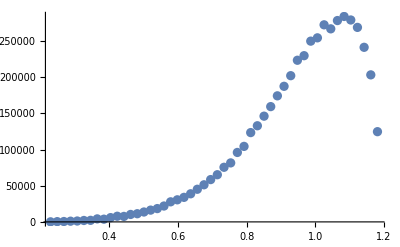

```mathematica
(**)
Clear[tab1, tab2, pic1, pic2];
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab1=ReadList["m2_234_test.txt",{Number,Number,Number}];
tab1=tab1[[All,1;;2]];
tab2=ReadList["m2_234.txt",{Number,Number,Number}];
tab2=tab2[[All,1;;2]];
pic1 = ListPlot[tab1];
pic2=ListPlot[tab2];
Show[pic1]
```

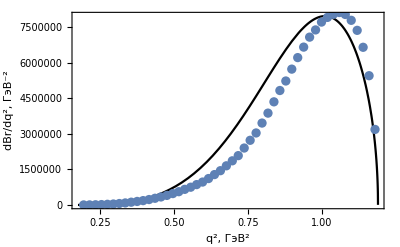

```mathematica
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab=ReadList["m2_234.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
{x,y}={tab[[43,1]],tab[[43,2]]};
y0=dΓ3π/.m232-> x;
pic1 = Plot[dΓ3π*y/y0,{m232,9 mπ^2,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab];
pic3 = Plot[dΓ3π1*y/y0,{m232,9 mπ^2,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
Show[pic3, pic2]
```

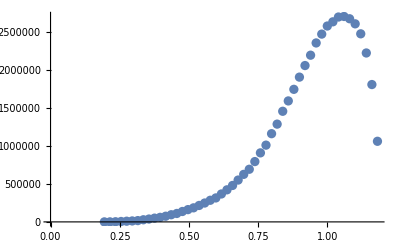

```mathematica
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab=ReadList["m2_234.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
pic2=ListPlot[tab]
```

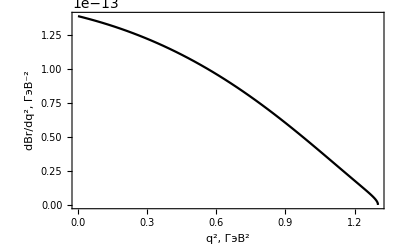

```mathematica
in="\\Xi_{cc}^{+}";
out="\\Xi_{c}^{0}";
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
picXi= Plot[dΓl,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ]
```

```mathematica
Show[picXi]
```

-Graphics-

```mathematica
Clear[tab1, tab2, pic1, pic2];
```

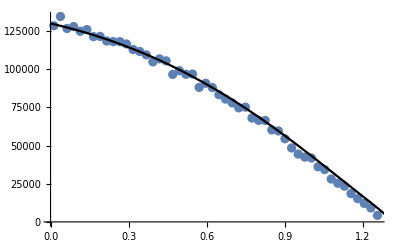

```mathematica
(**)
Clear[tab1, tab2, pic1, pic2];
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab1=ReadList["m2_23_test.txt",{Number,Number,Number}];
tab1=tab1[[All,1;;2]];
tab2=ReadList["m2_23.txt",{Number,Number,Number}];
tab2=tab2[[All,1;;2]];
pic1 = ListPlot[tab1];
pic2=ListPlot[tab2];
{x,y}={tab2[[10,1]],tab2[[10,2]]};
y0=dΓl/.m232-> x;
picXi1= Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
Show[pic2, picXi1 ]
```

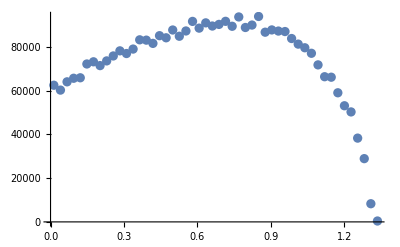

```mathematica
Clear[tab1, tab2, pic1, pic2];
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
tab3=ReadList["m2_23.txt",{Number,Number,Number}];
tab3=tab3[[All,1;;2]];
pic3 = ListPlot[tab3];
Show[pic3]
```